```mathematica
d[n_,0,a_]:=1
d[n_,1,a_]:=n-a+1
d[n_,k_,a_]:=Sum[Binomial[k,j]d[Floor[n/(m^j)],k-j,m+1],{j,1,k},{m,a,n^(1/k)}]

D32Unrolled[ n_ ] := -1 + Floor[ n^(1/3)]^3 + 3 Sum[ Floor[ n/(m^2)] - Floor[ Floor[n/m]^(1/2)]^2 + 2 Sum[ Floor[Floor[n/m]/j],{j,m+1,Floor[Floor[n/m]^(1/2)]}], {m,2,Floor[n^(1/3)]}]

D22Unrolled[ n_ ] := 1 - Floor[ n^(1/2)]^2 + 2 Sum [ Floor[ n/m],{m,2,Floor[n^(1/2)]}]
d0[n_,a_Integer] := 1
d1[n_, a_Integer] := n-a+1
d2a[n_, a_Integer] := Sum[ Binomial[ 2,2 ]d0[Floor[n/(m^2)],m+1] , {m,a,Floor[n^(1/2)]}]+
Sum[Binomial[ 2,1 ]d1[Floor[n/(m^1)],m+1], {m,a,Floor[n^(1/2)]}]
d2[n_, a_Integer] := 1 - 2 a + a^2 -Floor[ n^(1/2)]^2 + 2 Sum [ Floor[ n/m],{m,a,Floor[n^(1/2)]}]
d2[0,a_Integer] := 0
d3a[n_, a_Integer] := Sum[ Binomial[ 3,3 ]d0[Floor[n/(m^3)],m+1] , {m,a,Floor[n^(1/3)]}]+
Sum[Binomial[ 3,2 ]d1[Floor[n/(m^2)],m+1], {m,a,Floor[n^(1/3)]}]+
Sum[Binomial[ 3,1 ]d2a[Floor[n/(m^1)],m+1], {m,a,Floor[n^(1/3)]}]

d2e[n_, a_Integer] := (1-a)^2 -Floor[ n^(1/2)]^2 + 2 Sum [ Floor[ n/m],{m,a,Floor[n^(1/2)]}]
dd3e[n_, a_ ] := (1-a)^3+Floor[n^(1/3)]^3+Sum[3 Floor[n/s^2]-3 Floor[√Floor[n/s]]^2 + 6 Sum[ Floor[n/m/s],{m,s+1,Floor[Floor[n/s]^(1/2)]}],{s,a,Floor[n^(1/3)]}]
d4e[x_, b_ ] := 
(-1+b)^4+
-Floor[x^(1/4)]^4+
4 Sum[ Floor[x/(u^3)], {u, b, x^(1/4)}]+
-6 Sum[Floor[ Floor[x/(u^2)]^(1/2)]^2 ,{u, b, x^(1/4)}]+
12 Sum [  Floor[x/(u^2 m)], {u, b, x^(1/4)},{m,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}]+
4 Sum[Floor[Floor[x/u]^(1/3)]^3,{u, b, x^(1/4)}]+
12 Sum[ Floor[x/( u s^2)],{u, b, x^(1/4)},{s,(u+1),Floor[Floor[x/u]^(1/3)]}]+
-12Sum[ Floor[Floor[x/(u s)]^(1/2)]^2 ,{u, b, x^(1/4)},{s,(u+1),(x/u)^(1/3)}]+
24  Sum[  Floor[x/(u m s)],{u, b,x^(1/4)},{s,u+1,(x/u)^(1/3)},{m,s+1,(x/(u s))^(1/2)}]
```

```mathematica
d4e[100000,2]
```

11796070

```mathematica
d[100000,4,2]
```

11796070

```mathematica
FF[x_, b_ ]:= Sum[  Floor[x/(u m s)],{u, b,x^(1/4)},{s,u+1,(x/u)^(1/3)},{m,s+1,(x/(u s))^(1/2)}]
```

```mathematica
FF[10000,2]
```

21090

```mathematica
GG[x_, b_ ]:= Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,(x/u)^(1/3)},{m,2,(x/(u s))^(1/2)}]-
Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,(x/u)^(1/3)},{m,2,s}]-
Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,u},{m,2,(x/(u s))^(1/2)}]+
Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,u},{m,2,s}]-
Sum[  Floor[x/(u m s)],{u, 2,b-1},{s,2,(x/u)^(1/3)},{m,2,(x/(u s))^(1/2)}]+
Sum[  Floor[x/(u m s)],{u, 2,b-1},{s,2,(x/u)^(1/3)},{m,2,s}]+
Sum[  Floor[x/(u m s)],{u, 2,b-1},{s,2,u},{m,2,(x/(u s))^(1/2)}]-
Sum[  Floor[x/(u m s)],{u, 2,b-1},{s,2,u},{m,2,s}]
```

```mathematica
GG[10000,2]
```

21090

```mathematica
HH[x_, b_ ]:= Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,(x/u)^(1/3)},{m,2,(x/(u s))^(1/2)}]-
Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,(x/u)^(1/3)},{m,2,s}]-
Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,u},{m,2,(x/(u s))^(1/2)}]+
Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,u},{m,2,s}]-
Sum[  Floor[x/(u m s)],{u, 2,b-1},{s,2,(x/u)^(1/3)},{m,2,(x/(u s))^(1/2)}]+
Sum[  Floor[x/(u m s)],{u, 2,b-1},{s,2,(x/u)^(1/3)},{m,2,s}]+
Sum[  Floor[x/(u m s)],{u, 2,b-1},{s,2,u},{m,2,(x/(u s))^(1/2)}]-
Sum[  Floor[x/(u m s)],{u, 2,b-1},{s,2,u},{m,2,s}]
```

```mathematica
HH[10000,2]
```

21090

```mathematica
dd3f[n_, a_ ] := (1-a)^3+Floor[n^(1/3)]^3+
+3 Sum[Floor[n/(s^2)],{s,a,n^(1/3)}]+
-3 Sum[Floor[Floor[n/s]^(1/2)]^2 ,{s,a,n^(1/3)}]+
6 Sum[Floor[n/m/s],{s,a,n^(1/3)},{m,s+1,Floor[n/s]^(1/2)}]
```

```mathematica
dd3e[100,2]
```

324

```mathematica
dd3f[100,2]
```

324

```mathematica
II[x_ ]:= Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,(x/u)^(1/3)},{m,2,(x/(u s))^(1/2)}]-
Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,(x/u)^(1/3)},{m,2,s}]-
Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,u},{m,2,(x/(u s))^(1/2)}]+
Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,u},{m,2,s}]-
Sum[  Floor[x/(u m s)],{u, 2,1},{s,2,(x/u)^(1/3)},{m,2,(x/(u s))^(1/2)}]+
Sum[  Floor[x/(u m s)],{u, 2,1},{s,2,(x/u)^(1/3)},{m,2,s}]+
Sum[  Floor[x/(u m s)],{u, 2,1},{s,2,u},{m,2,(x/(u s))^(1/2)}]-
Sum[  Floor[x/(u m s)],{u, 2,1},{s,2,u},{m,2,s}]
```

```mathematica
II[10000]
```

21090

```mathematica
HH[x,2]
```

$Aborted

```mathematica
JJ[x_ ]:= Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,(x/u)^(1/3)},{m,2,(x/(u s))^(1/2)}]-
Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,(x/u)^(1/3)},{m,2,s}]-
Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,u},{m,2,(x/(u s))^(1/2)}]+
Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,u},{m,2,s}]
```

```mathematica
JJ[10000]
```

21090

```mathematica
KK[x_] := Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,2,u},{m,2,s}]
```

```mathematica
KK[10000]
```

17856

```mathematica
KK[x]
```

$Aborted

```mathematica
ddd[n_, a_] := Sum[Floor[n/m/s],{s,a,n^(1/3)},{m,s+1,Floor[n/s]^(1/2)}]
```

```mathematica
ddd[10000,2]
```

49245

```mathematica
eee[n_] := Sum[Floor[n/( m s )],{s,2,n^(1/3)},{m,2,Floor[n/s]^(1/2)}]-
Sum[Floor[n/( m s )],{s,2,n^(1/3)},{m,2,s}]
```

```mathematica
eee[10000]
```

49245

```mathematica
dd3p[n_, a_ ] := Sum[3 Floor[n/s^2]-3 Floor[√Floor[n/s]]^2 ,{s,a,Floor[n^(1/3)]}]
```

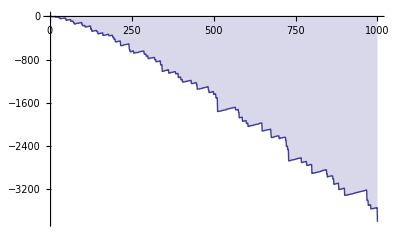

```mathematica
DiscretePlot[ dd3p[n,2],{n,2,1000}]
```

```mathematica
dd3pa[n_, a_ ] := Sum[3 Floor[n/s^2] ,{s,a,Floor[n^(1/3)]}]
```

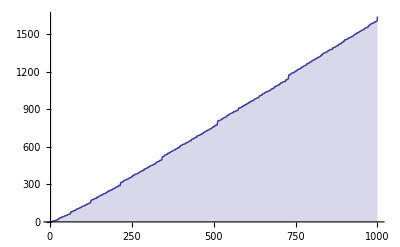

```mathematica
DiscretePlot[ dd3pa[n,2],{n,2,1000}]
```

```mathematica
dd3pb[n_, a_ ] := Sum[-3 Floor[√Floor[n/s]]^2 ,{s,a,Floor[n^(1/3)]}]
```

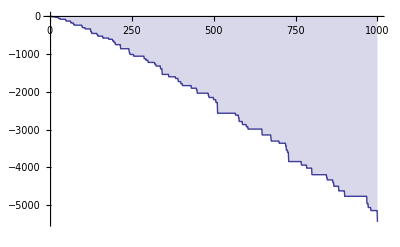

```mathematica
DiscretePlot[ dd3pb[n,2],{n,2,1000}]
```

```mathematica
dd3pc[n_, a_ ] := Floor[n^(1/3)]^3
```

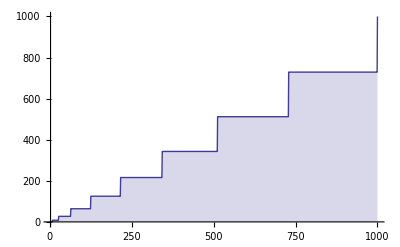

```mathematica
DiscretePlot[ dd3pc[n,2],{n,2,1000}]
```

```mathematica
dd3pd[n_, a_ ] := Sum[6 Sum[ Floor[n/m/s],{m,s+1,Floor[Floor[n/s]^(1/2)]}],{s,a,Floor[n^(1/3)]}]
```

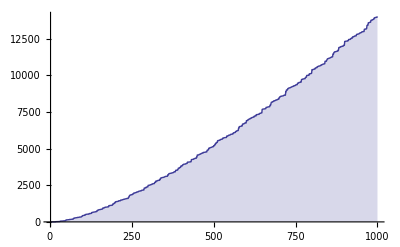

```mathematica
DiscretePlot[ dd3pd[n,2],{n,2,1000}]
```

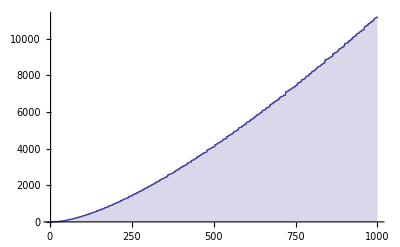

```mathematica
DiscretePlot[ dd3e[n,2],{n,2,1000}]
```

```mathematica
d3a[1000,2]
```

11217

```mathematica
D2k3Alt[200]
```

1027

```mathematica
D2k3[n_]:=Sum[1,{a,2,n},{b,2,n/a},{c,2,n/(a b)}]
D2k3Alt[n_] := 6 Sum[ 1,{a,2,n^(1/3)},{b,a+1,Floor[n/a]^(1/2)},{c,b+1,Floor[n/(a b)]}]+
3 Sum[ 1,{a,2,n^(1/3)},{b,a+1,Floor[n/a]^(1/2)}, {c,b,b}]+
3 Sum[ 1, {a,2,n^(1/3)},{b,a,a},{c,b+1,n/(a b )}]+
Sum[ 1, {a,2,n^(1/3)}, {b,a,a},{c,b,b}]
```

```mathematica
D2k3[200]
```

1027